# BoxWhiskerChart

### Basic examples

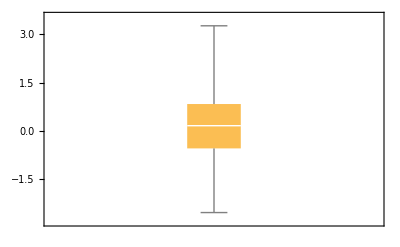

```mathematica
BoxWhiskerChart[RandomVariate[NormalDistribution[0,1],100]]
```

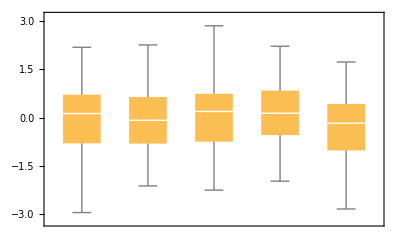

```mathematica
BoxWhiskerChart[Table[RandomVariate[NormalDistribution[0,1],100],5]]
```

```mathematica
data=Table[RandomVariate[NormalDistribution[μ,1],100],{μ,{0,3,2,5}},{2}];
```

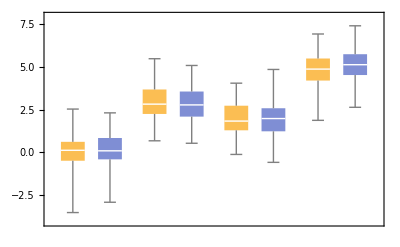

```mathematica
BoxWhiskerChart[data]
```

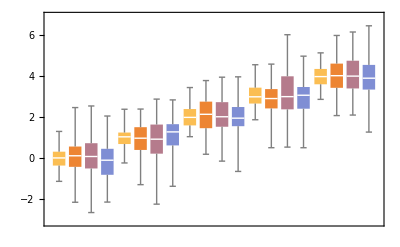

```mathematica
BoxWhiskerChart[Table[RandomVariate[NormalDistribution[μ,σ],100],{μ,{0,1,2,3,4}},{σ,{0.5,0.8,1.,0.9}}]]
```

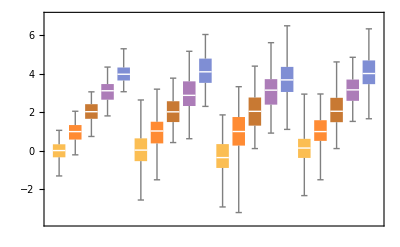

```mathematica
BoxWhiskerChart[Table[RandomVariate[NormalDistribution[μ,σ],100],{σ,{0.5,0.8,1.,0.9}},{μ,{0,1,2,3,4}}]]
```

## References

```mathematica
?NormalDistribution
```

NormalDistribution[μ,σ] represents a normal (Gaussian) distribution with mean μ and standard deviation σ.
NormalDistribution[] represents a normal distribution with zero mean and unit standard deviation.

```mathematica
?BoxWhiskerChart
```

BoxWhiskerChart[{x_1,x_2,…}] makes a box-and-whisker chart for the values x_i.
BoxWhiskerChart[{x_1,x_2,…},bwspec] makes a chart with box-and-whisker symbol specification bwspec.
BoxWhiskerChart[{data_1,data_2,…},…] makes a chart with box-and-whisker symbol for each data_i.
BoxWhiskerChart[{{data_1,data_2,…},…},…] makes a box-and-whisker chart from multiple groups of datasets {data_1,data_2,…}.

```mathematica
?RandomVariate
```

RandomVariate[dist] gives a pseudorandom variate from the symbolic distribution dist.
RandomVariate[dist,n] gives a list of n pseudorandom variates from the symbolic distribution dist.
RandomVariate[dist,{n_1,n_2,…}] gives an n_1× n_2×… array of pseudorandom variates from the symbolic distribution dist.